```mathematica
(*(ccdata[7]/.{x_,y_}/;x>maxyx->{x,0})[[All,2]]*)
```

```mathematica
SetDirectory[ParentDirectory[NotebookDirectory[]]];
```

## Define Functions

```mathematica
BW[w_,wr_,Γ_,δbg_,const_,shift_,shift2_]:=
const((Γ/2)^2/((w-wr)^2+(Γ/2)^2))+ δbg((Γ/2)(w-wr))/((w-wr)^2+(Γ/2)^2)+0 ((4 (w-wr)^2- Γ^2) deltabg^2)/(4 (w-wr)^2+Γ^2)+shift (w-wr)+shift2 ;
BWi[w_,wr_,Γ_,const_]:=const((Γ/2)^2/((w-wr)^2+(Γ/2)^2)) ;

fitnew[input_,output_,Tscan_]:=Module[{temp=Range[1,Length[Tscan]],n,maxx,minx,maxy,maxyx,maxyi,maxxy,inter,maxxs,maxxis,maxys,mins,hwhmi,gammas,inputc,bad},
SetSharedVariable[temp];
ParallelDo[n=temp[[ii]];
maxx=Max[input[n][[All,1]]];
minx=Min[input[n][[All,1]]];
maxy=Max[input[n][[All,2]]];
maxyx=input[n][[Position[input[n],Max[input[n][[All,2]]]][[1,1]],1]];
maxyi=Position[input[n][[All,1]],maxyx][[1,1]];
maxxy=input[n][[Position[input[n],Max[input[n][[All,1]]]][[1,1]],2]];
inter=Interpolation[input[n],InterpolationOrder->1];maxxs=Sort[Quiet[DeleteDuplicatesBy[Table[{Round[FindMaxValue[{inter[x],maxyx≤x≤maxx},{x,a}],maxxy],FindArgMax[{inter[x],maxyx≤x≤maxx},{x,a}][[1]]},{a,maxyx,maxx,(maxx-maxyx)/50}],First][[All,2]]]];
bad={};
If[Length[maxxs]>1,Do[If[maxxs[[i+1]]/maxxs[[i]]≤1.001,bad=Append[bad,{i}]],{i,Length[maxxs]-1}]];
maxxs=Delete[maxxs,bad];maxxis=Sort[Table[Position[input[n][[All,1]],Nearest[input[n][[All,1]],maxxs[[i]]][[1]]][[1,1]],{i,Length[maxxs]}]];
bad={};
Do[If[Or[input[n][[maxxis[[i]]-30,2]]>input[n][[maxxis[[i]],2]],input[n][[maxxis[[i]]+30,2]]>input[n][[maxxis[[i]],2]]],bad=Append[bad,{i}]],{i,Length[maxxis]}];maxxs=Delete[maxxs,bad];maxxis=Delete[maxxis,bad];
maxys=Table[input[n][[maxxis[[i]],2]],{i,Length[maxxs]}];
If[Length[maxxs]>1,
mins=Range[Length[maxxs]-1];
Do[mins[[i]]=Position[input[n][[All,2]],Min[input[n][[maxxis[[i]];;maxxis[[i+1]],2]]]][[1,1]],{i,Length[maxxs]-1}];mins=Append[Prepend[mins,maxxis[[1]]-(mins[[1]]-maxxis[[1]])],If[maxxis[[-1]]+(maxxis[[-1]]-mins[[-1]])≤ Length[input[n]],maxxis[[-1]]+(maxxis[[-1]]-mins[[-1]]),Length[input[n]]]];,
hwhmi=Position[input[n],Nearest[input[n][[;;maxyi,2]],maxy/2][[1]]][[1,1]];
mins={maxyi-3(maxyi-hwhmi),If[maxyi+3(maxyi-hwhmi)≤Length[input[n]],maxyi+3(maxyi-hwhmi),Length[input[n]]]};];
If[mins[[1]]<0,mins[[1]]=1];
hwhmi=Range[Length[maxxs]];
Do[hwhmi[[i]]=Position[input[n],Nearest[input[n][[mins[[i]];;maxxis[[i]],2]],inter[maxxs[[i]]]/2][[1]]][[1,1]],{i,Length[maxxs]}];
gammas=Range[Length[hwhmi]];
Do[gammas[[i]]=2(maxxs[[i]]-input[n][[hwhmi[[i]],1]]),{i,Length[hwhmi]}];
inputc=Range[Length[maxxs]];
Do[inputc[[i]]=input[n][[If[i≥2,If[maxxis[[i]]-3(maxxis[[i]]-hwhmi[[i]])<mins[[i]],mins[[i]],maxxis[[i]]-3(maxxis[[i]]-hwhmi[[i]])],If[maxxis[[i]]-3(maxxis[[i]]-hwhmi[[i]])>0,maxxis[[i]]-3(maxxis[[i]]-hwhmi[[i]]),1]];;If[maxxis[[i]]+3(maxxis[[i]]-hwhmi[[i]])<mins[[i+1]],maxxis[[i]]+3(maxxis[[i]]-hwhmi[[i]]),mins[[i+1]]]]],{i,Length[maxxs]}];
temp[[ii]]=Range[Length[hwhmi]];
Do[temp[[ii,i]]=NonlinearModelFit[inputc[[i]],{BW[w,wr,Γ,δbg,const,shift,shift2],const>0,Γ>0},{{wr,maxxs[[i]]},{Γ,gammas[[i]]},{const,maxys[[i]]},{δbg,0.0},{shift,0.0},{shift2,0.0}},w,MaxIterations->1000],{i,Length[hwhmi]}];Print[ii];,{ii,Length[Tscan]}];output=temp;];

store[param_,res_,model_]:=Module[{temp=ToString[res]},res=Range[Length[model]];
Do[res[[i]]=Range[Length[model[[i]]]],{i,Length[model]}];Do[Do[res[[i,ii]]=param/.model[[i,ii]]["BestFitParameters"],{ii,Length[res[[i]]]}],{i,Length[res]}];Export["spectraldata/Tscan/results/"<>temp<>".dat",res];];

storearea[res_,model_]:=Module[{temp=ToString[res]},res=Range[Length[model]];
Do[res[[i]]=Range[Length[model[[i]]]],{i,Length[model]}];Do[Do[res[[i,ii]]=π/2(Γ/.model[[i,ii]]["BestFitParameters"])( const/.model[[i,ii]]["BestFitParameters"]),{ii,Length[res[[i]]]}],{i,Length[res]}];Export["spectraldata/Tscan/results/"<>temp<>".dat",res];];

import[res_]:=res=Import["spectraldata/Tscan/results/"<>ToString[res]<>".dat"];
```

## Charmonium

### Import Data

```mathematica
Tscanc=Round[1000 Join[Table[i,{i,0.15,0.16,0.001}],{0.162},Table[i,{i,0.164,0.170,0.003}],Table[i,{i,0.1740,0.2220,0.003}],Table[i,{i,0.224,0.230,0.003}],Table[i,{i,0.234,0.249,0.003}],Table[i,{i,0.253,0.3,0.003}]]]
```

{150,151,152,153,154,155,156,157,158,159,160,162,164,167,170,174,177,180,183,186,189,192,195,198,201,204,207,210,213,216,219,222,224,227,230,234,237,240,243,246,249,253,256,259,262,265,268,271,274,277,280,283,286,289,292,295,298}

```mathematica
Do[ccdata[n]=Import["spectraldata/Tscan/cc/swccT"<>ToString[Tscanc[[n]]]<>"spectra.dat"];,{n,Length[Tscanc]}];
Manipulate[ListPlot[ccdata[n],Joined->True],{n,1,Length[Tscanc],1}]
```

ListPlot::lpn: ccdata[1.] is not a list of numbers or pairs of numbers.

```mathematica
Do[ccdatau[n]=Import["spectraldata/Tscan/cc/swccT"<>ToString[Tscanc[[n]]]<>"uspectra.dat"];,{n,Length[Tscanc]}];
Manipulate[ListPlot[ccdatau[n],Joined->True],{n,1,Length[Tscanc],1}]
```

ListPlot::lpn: ccdatau[1.] is not a list of numbers or pairs of numbers.

```mathematica
Do[ccdatal[n]=Import["spectraldata/Tscan/cc/swccT"<>ToString[Tscanc[[n]]]<>"lspectra.dat"];,{n,Length[Tscanc]}];
Manipulate[ListPlot[ccdatal[n],Joined->True],{n,1,Length[Tscanc],1}]
```

ListPlot::lpn: ccdatal[1.] is not a list of numbers or pairs of numbers.

### Fitting

```mathematica
Clear[ccmodelu,ccmodell,ccmodel]
fitnew[ccdata,ccmodel,Tscanc];
fitnew[ccdatal,ccmodell,Tscanc];
fitnew[ccdatau,ccmodelu,Tscanc];
```

### Store Results

```mathematica
Do[If[Length[ccmodel[[i]]]>2,ccmodel[[i]]=ccmodel[[i,;;2]]];If[Length[ccmodelu[[i]]]>2,ccmodelu[[i]]=ccmodelu[[i,;;2]]];If[Length[ccmodell[[i]]]>2,ccmodell[[i]]=ccmodell[[i,;;2]]];,{i,Length[ccmodel]}];
```

```mathematica
Clear[wrfitcc,wrfitccl,wrfitccu,gfitcc,gfitccl,gfitccu,areafitcc,areafitccu,areafitccl,cfitcc,cfitccl,cfitccu,dfitcc,dfitccl,dfitccu,sfitcc,sfitccl,sfitccu,s2fitcc,s2fitccl,s2fitccu];
store[wr,wrfitcc,ccmodel];
store[wr,wrfitccl,ccmodell];
store[wr,wrfitccu,ccmodelu];
store[Γ,gfitcc,ccmodel];
store[Γ,gfitccl,ccmodell];
store[Γ,gfitccu,ccmodelu];
store[const,cfitcc,ccmodel];
store[const,cfitccl,ccmodell];
store[const,cfitccu,ccmodelu];
store[δbg,dfitcc,ccmodel];
store[δbg,dfitccl,ccmodell];
store[δbg,dfitccu,ccmodelu];
store[shift,sfitcc,ccmodel];
store[shift,sfitccl,ccmodell];
store[shift,sfitccu,ccmodelu];
store[shift2,s2fitcc,ccmodel];
store[shift2,s2fitccl,ccmodell];
store[shift2,s2fitccu,ccmodelu];
storearea[areafitcc,ccmodel];
storearea[areafitccl,ccmodell];
storearea[areafitccu,ccmodelu];
```

### Display Results

```mathematica
import[wrfitcc];
import[wrfitccl];
import[wrfitccu];
import[gfitcc];
import[gfitccl];
import[gfitccu];
import[cfitcc];
import[cfitccl];
import[cfitccu];
import[dfitcc];
import[dfitccl];
import[dfitccu];
import[sfitcc];
import[sfitccl];
import[sfitccu];
import[s2fitcc];
import[s2fitccl];
import[s2fitccu];
import[areafitcc];
import[areafitccl];
import[areafitccu];
```

```mathematica
Do[If[Length[wrfitcc[[-i]]]<2,cc1Tcut=Length[wrfitcc]-i];,{i,Length[wrfitcc]}];
Do[If[Length[wrfitccu[[-i]]]<2,cc1uTcut=Length[wrfitccu]-i];,{i,Length[wrfitccl]}];
Do[If[Length[wrfitccl[[-i]]]<2,cc1lTcut=Length[wrfitccl]-i];,{i,Length[wrfitccu]}];
```

```mathematica
Manipulate[Show[{ListPlot[ccdata[i],Joined->True],Plot[BW[x,wrfitcc[[i,ii]],gfitcc[[i,ii]],dfitcc[[i,ii]],cfitcc[[i,ii]],sfitcc[[i,ii]],s2fitcc[[i,ii]]],{x,0.7wrfitcc[[i,ii]],1.3wrfitcc[[i,ii]]},PlotStyle->{Red,Dashed},PlotRange->All],Plot[BWi[x,wrfitcc[[i,ii]],gfitcc[[i,ii]],cfitcc[[i,ii]]],{x,0.7wrfitcc[[i,ii]],1.3wrfitcc[[i,ii]]},PlotStyle->{Green,Dashed},PlotRange->All]}],{i,1,Length[wrfitcc],1},{ii,1,Length[wrfitcc[[1]]],1}]
```

ListPlot::lpn: ccdata[1.] is not a list of numbers or pairs of numbers.

Part::partd: Part specification wrfitcc⟦1,1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Plot::plln: Limiting value 0.7 wrfitcc⟦1,1⟧ in {x,0.7 wrfitcc⟦1,1⟧,1.3 wrfitcc⟦1,1⟧} is not a machine-sized real number.

Show::gcomb: Could not combine the graphics objects in Show[{ListPlot[ccdata[1],Joined→True],Plot[BW[x,wrfitcc⟦FE`i$$25,FE`ii$$25⟧,gfitcc⟦FE`i$$25,FE`ii$$25⟧,dfitcc⟦FE`i$$25,FE`ii$$25⟧,cfitcc⟦FE`i$$25,FE`ii$$25⟧,sfitcc⟦FE`i$$25,FE`ii$$25⟧,s2fitcc⟦FE`i$$25,FE`ii$$25⟧],{x,0.7 wrfitcc⟦FE`i$$25,FE`ii$$25⟧,1.3 wrfitcc⟦FE`i$$25,FE`ii$$25⟧},PlotStyle→{Red,Dashed},PlotRange→All],Plot[BWi[x,wrfitcc⟦FE`i$$25,FE`ii$$25⟧,gfitcc⟦FE`i$$25,FE`ii$$25⟧,cfitcc⟦FE`i$$25,FE`ii$$25⟧],{x,0.7 wrfitcc⟦FE`i$$25,FE`ii$$25⟧,1.3 wrfitcc⟦FE`i$$25,FE`ii$$25⟧},PlotStyle→{Green,Dashed},PlotRange→All]}].

Plot::plln: Limiting value 0.7 wrfitcc⟦1,1⟧ in {x,0.7 wrfitcc⟦1,1⟧,1.3 wrfitcc⟦1,1⟧} is not a machine-sized real number.

General::stop: Further output of Plot::plln will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in Show[{ListPlot[ccdata[1],Joined→True],Plot[BW[x,wrfitcc⟦FE`i$$25,FE`ii$$25⟧,gfitcc⟦FE`i$$25,FE`ii$$25⟧,dfitcc⟦FE`i$$25,FE`ii$$25⟧,cfitcc⟦FE`i$$25,FE`ii$$25⟧,sfitcc⟦FE`i$$25,FE`ii$$25⟧,s2fitcc⟦FE`i$$25,FE`ii$$25⟧],{x,0.7 wrfitcc⟦FE`i$$25,FE`ii$$25⟧,1.3 wrfitcc⟦FE`i$$25,FE`ii$$25⟧},PlotStyle→{Red,Dashed},PlotRange→All],Plot[BWi[x,wrfitcc⟦FE`i$$25,FE`ii$$25⟧,gfitcc⟦FE`i$$25,FE`ii$$25⟧,cfitcc⟦FE`i$$25,FE`ii$$25⟧],{x,0.7 wrfitcc⟦FE`i$$25,FE`ii$$25⟧,1.3 wrfitcc⟦FE`i$$25,FE`ii$$25⟧},PlotStyle→{Green,Dashed},PlotRange→All]}].

ListPlot::lpn: ccdata[1.] is not a list of numbers or pairs of numbers.

Part::partd: Part specification wrfitcc⟦1,1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Plot::plln: Limiting value 0.7 wrfitcc⟦1,1⟧ in {x,0.7 wrfitcc⟦1,1⟧,1.3 wrfitcc⟦1,1⟧} is not a machine-sized real number.

Show::gcomb: Could not combine the graphics objects in Show[{ListPlot[ccdata[1],Joined→True],Plot[BW[x,wrfitcc⟦FE`i$$23,FE`ii$$23⟧,gfitcc⟦FE`i$$23,FE`ii$$23⟧,dfitcc⟦FE`i$$23,FE`ii$$23⟧,cfitcc⟦FE`i$$23,FE`ii$$23⟧,sfitcc⟦FE`i$$23,FE`ii$$23⟧,s2fitcc⟦FE`i$$23,FE`ii$$23⟧],{x,0.7 wrfitcc⟦FE`i$$23,FE`ii$$23⟧,1.3 wrfitcc⟦FE`i$$23,FE`ii$$23⟧},PlotStyle→{Red,Dashed},PlotRange→All],Plot[BWi[x,wrfitcc⟦FE`i$$23,FE`ii$$23⟧,gfitcc⟦FE`i$$23,FE`ii$$23⟧,cfitcc⟦FE`i$$23,FE`ii$$23⟧],{x,0.7 wrfitcc⟦FE`i$$23,FE`ii$$23⟧,1.3 wrfitcc⟦FE`i$$23,FE`ii$$23⟧},PlotStyle→{Green,Dashed},PlotRange→All]}].

Plot::plln: Limiting value 0.7 wrfitcc⟦1,1⟧ in {x,0.7 wrfitcc⟦1,1⟧,1.3 wrfitcc⟦1,1⟧} is not a machine-sized real number.

General::stop: Further output of Plot::plln will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in Show[{ListPlot[ccdata[1],Joined→True],Plot[BW[x,wrfitcc⟦FE`i$$23,FE`ii$$23⟧,gfitcc⟦FE`i$$23,FE`ii$$23⟧,dfitcc⟦FE`i$$23,FE`ii$$23⟧,cfitcc⟦FE`i$$23,FE`ii$$23⟧,sfitcc⟦FE`i$$23,FE`ii$$23⟧,s2fitcc⟦FE`i$$23,FE`ii$$23⟧],{x,0.7 wrfitcc⟦FE`i$$23,FE`ii$$23⟧,1.3 wrfitcc⟦FE`i$$23,FE`ii$$23⟧},PlotStyle→{Red,Dashed},PlotRange→All],Plot[BWi[x,wrfitcc⟦FE`i$$23,FE`ii$$23⟧,gfitcc⟦FE`i$$23,FE`ii$$23⟧,cfitcc⟦FE`i$$23,FE`ii$$23⟧],{x,0.7 wrfitcc⟦FE`i$$23,FE`ii$$23⟧,1.3 wrfitcc⟦FE`i$$23,FE`ii$$23⟧},PlotStyle→{Green,Dashed},PlotRange→All]}].

```mathematica
Manipulate[Show[{ListPlot[ccdatau[i],Joined->True],Plot[BW[x,wrfitccu[[i,ii]],gfitccu[[i,ii]],dfitccu[[i,ii]],cfitccu[[i,ii]],sfitccu[[i,ii]],s2fitccu[[i,ii]]],{x,0.7wrfitccu[[i,ii]],1.3wrfitccu[[i,ii]]},PlotStyle->{Red,Dashed},PlotRange->All],Plot[BWi[x,wrfitccu[[i,ii]],gfitccu[[i,ii]],cfitccu[[i,ii]]],{x,0.7wrfitccu[[i,ii]],1.3wrfitccu[[i,ii]]},PlotStyle->{Green,Dashed},PlotRange->All]}],{i,1,Length[wrfitccu],1},{ii,1,Length[wrfitccu[[1]]],1}]
```

ListPlot::lpn: ccdatau[1.] is not a list of numbers or pairs of numbers.

Part::partd: Part specification wrfitccu⟦1,1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Plot::plln: Limiting value 0.7 wrfitccu⟦1,1⟧ in {x,0.7 wrfitccu⟦1,1⟧,1.3 wrfitccu⟦1,1⟧} is not a machine-sized real number.

Show::gcomb: Could not combine the graphics objects in Show[{ListPlot[ccdatau[1],Joined→True],Plot[BW[x,wrfitccu⟦FE`i$$28,FE`ii$$28⟧,gfitccu⟦FE`i$$28,FE`ii$$28⟧,dfitccu⟦FE`i$$28,FE`ii$$28⟧,cfitccu⟦FE`i$$28,FE`ii$$28⟧,sfitccu⟦FE`i$$28,FE`ii$$28⟧,s2fitccu⟦FE`i$$28,FE`ii$$28⟧],{x,0.7 wrfitccu⟦FE`i$$28,FE`ii$$28⟧,1.3 wrfitccu⟦FE`i$$28,FE`ii$$28⟧},PlotStyle→{Red,Dashed},PlotRange→All],Plot[BWi[x,wrfitccu⟦FE`i$$28,FE`ii$$28⟧,gfitccu⟦FE`i$$28,FE`ii$$28⟧,cfitccu⟦FE`i$$28,FE`ii$$28⟧],{x,0.7 wrfitccu⟦FE`i$$28,FE`ii$$28⟧,1.3 wrfitccu⟦FE`i$$28,FE`ii$$28⟧},PlotStyle→{Green,Dashed},PlotRange→All]}].

Plot::plln: Limiting value 0.7 wrfitccu⟦1,1⟧ in {x,0.7 wrfitccu⟦1,1⟧,1.3 wrfitccu⟦1,1⟧} is not a machine-sized real number.

General::stop: Further output of Plot::plln will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in Show[{ListPlot[ccdatau[1],Joined→True],Plot[BW[x,wrfitccu⟦FE`i$$28,FE`ii$$28⟧,gfitccu⟦FE`i$$28,FE`ii$$28⟧,dfitccu⟦FE`i$$28,FE`ii$$28⟧,cfitccu⟦FE`i$$28,FE`ii$$28⟧,sfitccu⟦FE`i$$28,FE`ii$$28⟧,s2fitccu⟦FE`i$$28,FE`ii$$28⟧],{x,0.7 wrfitccu⟦FE`i$$28,FE`ii$$28⟧,1.3 wrfitccu⟦FE`i$$28,FE`ii$$28⟧},PlotStyle→{Red,Dashed},PlotRange→All],Plot[BWi[x,wrfitccu⟦FE`i$$28,FE`ii$$28⟧,gfitccu⟦FE`i$$28,FE`ii$$28⟧,cfitccu⟦FE`i$$28,FE`ii$$28⟧],{x,0.7 wrfitccu⟦FE`i$$28,FE`ii$$28⟧,1.3 wrfitccu⟦FE`i$$28,FE`ii$$28⟧},PlotStyle→{Green,Dashed},PlotRange→All]}].

ListPlot::lpn: ccdatau[1.] is not a list of numbers or pairs of numbers.

Part::partd: Part specification wrfitccu⟦1,1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Plot::plln: Limiting value 0.7 wrfitccu⟦1,1⟧ in {x,0.7 wrfitccu⟦1,1⟧,1.3 wrfitccu⟦1,1⟧} is not a machine-sized real number.

Show::gcomb: Could not combine the graphics objects in Show[{ListPlot[ccdatau[1],Joined→True],Plot[BW[x,wrfitccu⟦FE`i$$26,FE`ii$$26⟧,gfitccu⟦FE`i$$26,FE`ii$$26⟧,dfitccu⟦FE`i$$26,FE`ii$$26⟧,cfitccu⟦FE`i$$26,FE`ii$$26⟧,sfitccu⟦FE`i$$26,FE`ii$$26⟧,s2fitccu⟦FE`i$$26,FE`ii$$26⟧],{x,0.7 wrfitccu⟦FE`i$$26,FE`ii$$26⟧,1.3 wrfitccu⟦FE`i$$26,FE`ii$$26⟧},PlotStyle→{Red,Dashed},PlotRange→All],Plot[BWi[x,wrfitccu⟦FE`i$$26,FE`ii$$26⟧,gfitccu⟦FE`i$$26,FE`ii$$26⟧,cfitccu⟦FE`i$$26,FE`ii$$26⟧],{x,0.7 wrfitccu⟦FE`i$$26,FE`ii$$26⟧,1.3 wrfitccu⟦FE`i$$26,FE`ii$$26⟧},PlotStyle→{Green,Dashed},PlotRange→All]}].

Plot::plln: Limiting value 0.7 wrfitccu⟦1,1⟧ in {x,0.7 wrfitccu⟦1,1⟧,1.3 wrfitccu⟦1,1⟧} is not a machine-sized real number.

General::stop: Further output of Plot::plln will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in Show[{ListPlot[ccdatau[1],Joined→True],Plot[BW[x,wrfitccu⟦FE`i$$26,FE`ii$$26⟧,gfitccu⟦FE`i$$26,FE`ii$$26⟧,dfitccu⟦FE`i$$26,FE`ii$$26⟧,cfitccu⟦FE`i$$26,FE`ii$$26⟧,sfitccu⟦FE`i$$26,FE`ii$$26⟧,s2fitccu⟦FE`i$$26,FE`ii$$26⟧],{x,0.7 wrfitccu⟦FE`i$$26,FE`ii$$26⟧,1.3 wrfitccu⟦FE`i$$26,FE`ii$$26⟧},PlotStyle→{Red,Dashed},PlotRange→All],Plot[BWi[x,wrfitccu⟦FE`i$$26,FE`ii$$26⟧,gfitccu⟦FE`i$$26,FE`ii$$26⟧,cfitccu⟦FE`i$$26,FE`ii$$26⟧],{x,0.7 wrfitccu⟦FE`i$$26,FE`ii$$26⟧,1.3 wrfitccu⟦FE`i$$26,FE`ii$$26⟧},PlotStyle→{Green,Dashed},PlotRange→All]}].

```mathematica
Manipulate[Show[{ListPlot[ccdatal[i],Joined->True],Plot[BW[x,wrfitccl[[i,ii]],gfitccl[[i,ii]],dfitccl[[i,ii]],cfitccl[[i,ii]],sfitccl[[i,ii]],s2fitccl[[i,ii]]],{x,0.7wrfitccl[[i,ii]],1.3wrfitccl[[i,ii]]},PlotStyle->{Red,Dashed},PlotRange->All],Plot[BWi[x,wrfitccl[[i,ii]],gfitccl[[i,ii]],cfitccl[[i,ii]]],{x,0.7wrfitccl[[i,ii]],1.3wrfitccl[[i,ii]]},PlotStyle->{Green,Dashed},PlotRange->All]}],{i,1,Length[wrfitccl],1},{ii,1,Length[wrfitccl[[1]]],1}]
```

ListPlot::lpn: ccdatal[1.] is not a list of numbers or pairs of numbers.

Part::partd: Part specification wrfitccl⟦1,1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Plot::plln: Limiting value 0.7 wrfitccl⟦1,1⟧ in {x,0.7 wrfitccl⟦1,1⟧,1.3 wrfitccl⟦1,1⟧} is not a machine-sized real number.

Show::gcomb: Could not combine the graphics objects in Show[{ListPlot[ccdatal[1],Joined→True],Plot[BW[x,wrfitccl⟦FE`i$$31,FE`ii$$31⟧,gfitccl⟦FE`i$$31,FE`ii$$31⟧,dfitccl⟦FE`i$$31,FE`ii$$31⟧,cfitccl⟦FE`i$$31,FE`ii$$31⟧,sfitccl⟦FE`i$$31,FE`ii$$31⟧,s2fitccl⟦FE`i$$31,FE`ii$$31⟧],{x,0.7 wrfitccl⟦FE`i$$31,FE`ii$$31⟧,1.3 wrfitccl⟦FE`i$$31,FE`ii$$31⟧},PlotStyle→{Red,Dashed},PlotRange→All],Plot[BWi[x,wrfitccl⟦FE`i$$31,FE`ii$$31⟧,gfitccl⟦FE`i$$31,FE`ii$$31⟧,cfitccl⟦FE`i$$31,FE`ii$$31⟧],{x,0.7 wrfitccl⟦FE`i$$31,FE`ii$$31⟧,1.3 wrfitccl⟦FE`i$$31,FE`ii$$31⟧},PlotStyle→{Green,Dashed},PlotRange→All]}].

Plot::plln: Limiting value 0.7 wrfitccl⟦1,1⟧ in {x,0.7 wrfitccl⟦1,1⟧,1.3 wrfitccl⟦1,1⟧} is not a machine-sized real number.

General::stop: Further output of Plot::plln will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in Show[{ListPlot[ccdatal[1],Joined→True],Plot[BW[x,wrfitccl⟦FE`i$$31,FE`ii$$31⟧,gfitccl⟦FE`i$$31,FE`ii$$31⟧,dfitccl⟦FE`i$$31,FE`ii$$31⟧,cfitccl⟦FE`i$$31,FE`ii$$31⟧,sfitccl⟦FE`i$$31,FE`ii$$31⟧,s2fitccl⟦FE`i$$31,FE`ii$$31⟧],{x,0.7 wrfitccl⟦FE`i$$31,FE`ii$$31⟧,1.3 wrfitccl⟦FE`i$$31,FE`ii$$31⟧},PlotStyle→{Red,Dashed},PlotRange→All],Plot[BWi[x,wrfitccl⟦FE`i$$31,FE`ii$$31⟧,gfitccl⟦FE`i$$31,FE`ii$$31⟧,cfitccl⟦FE`i$$31,FE`ii$$31⟧],{x,0.7 wrfitccl⟦FE`i$$31,FE`ii$$31⟧,1.3 wrfitccl⟦FE`i$$31,FE`ii$$31⟧},PlotStyle→{Green,Dashed},PlotRange→All]}].

ListPlot::lpn: ccdatal[1.] is not a list of numbers or pairs of numbers.

Part::partd: Part specification wrfitccl⟦1,1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Plot::plln: Limiting value 0.7 wrfitccl⟦1,1⟧ in {x,0.7 wrfitccl⟦1,1⟧,1.3 wrfitccl⟦1,1⟧} is not a machine-sized real number.

Show::gcomb: Could not combine the graphics objects in Show[{ListPlot[ccdatal[1],Joined→True],Plot[BW[x,wrfitccl⟦FE`i$$29,FE`ii$$29⟧,gfitccl⟦FE`i$$29,FE`ii$$29⟧,dfitccl⟦FE`i$$29,FE`ii$$29⟧,cfitccl⟦FE`i$$29,FE`ii$$29⟧,sfitccl⟦FE`i$$29,FE`ii$$29⟧,s2fitccl⟦FE`i$$29,FE`ii$$29⟧],{x,0.7 wrfitccl⟦FE`i$$29,FE`ii$$29⟧,1.3 wrfitccl⟦FE`i$$29,FE`ii$$29⟧},PlotStyle→{Red,Dashed},PlotRange→All],Plot[BWi[x,wrfitccl⟦FE`i$$29,FE`ii$$29⟧,gfitccl⟦FE`i$$29,FE`ii$$29⟧,cfitccl⟦FE`i$$29,FE`ii$$29⟧],{x,0.7 wrfitccl⟦FE`i$$29,FE`ii$$29⟧,1.3 wrfitccl⟦FE`i$$29,FE`ii$$29⟧},PlotStyle→{Green,Dashed},PlotRange→All]}].

Plot::plln: Limiting value 0.7 wrfitccl⟦1,1⟧ in {x,0.7 wrfitccl⟦1,1⟧,1.3 wrfitccl⟦1,1⟧} is not a machine-sized real number.

General::stop: Further output of Plot::plln will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in Show[{ListPlot[ccdatal[1],Joined→True],Plot[BW[x,wrfitccl⟦FE`i$$29,FE`ii$$29⟧,gfitccl⟦FE`i$$29,FE`ii$$29⟧,dfitccl⟦FE`i$$29,FE`ii$$29⟧,cfitccl⟦FE`i$$29,FE`ii$$29⟧,sfitccl⟦FE`i$$29,FE`ii$$29⟧,s2fitccl⟦FE`i$$29,FE`ii$$29⟧],{x,0.7 wrfitccl⟦FE`i$$29,FE`ii$$29⟧,1.3 wrfitccl⟦FE`i$$29,FE`ii$$29⟧},PlotStyle→{Red,Dashed},PlotRange→All],Plot[BWi[x,wrfitccl⟦FE`i$$29,FE`ii$$29⟧,gfitccl⟦FE`i$$29,FE`ii$$29⟧,cfitccl⟦FE`i$$29,FE`ii$$29⟧],{x,0.7 wrfitccl⟦FE`i$$29,FE`ii$$29⟧,1.3 wrfitccl⟦FE`i$$29,FE`ii$$29⟧},PlotStyle→{Green,Dashed},PlotRange→All]}].

```mathematica
cccont={3.648553230970728,3.628792315589096,3.6102772374036665,3.592872558615657,3.576462604611754,3.5609479062546994,3.5462423968160763,3.5322711829829765,3.5189687484274836,3.50627749401972,3.4941465499919833,3.471390082559803,3.4404770981602106,3.412745256022291,3.3876075252547677,3.364618948412143,3.3434352822109226,3.323785454856247,3.3054526994473723,3.288261308642187,3.272067135253791,3.2567506466093215,3.2422117602027,3.2283659447979494,3.2151412362308114,3.2027178984093014,3.191176351511658,3.1800210358114978,3.1692213413581785,3.158750046801837,3.1485828474763107,3.138697962475392,3.1290758041221385,3.1196986990116966,3.1105506514104317,3.1016171414292035,3.0928849538048953,3.0843420286931376,3.0759773300200837,3.067780741067037,3.0597429617989613,3.051855425801331,3.0441102296733202,3.0365000618906883,3.0290181515134766,3.0216582135930583,3.0144144050429746,3.00728128686385,3.00025378432098,2.9933271604368104,2.9864969822394043,2.979759099825311,2.973109619884775,2.966544887282899,2.9600614652455026,2.9536561196905122,2.947325800789547};
```

```mathematica
cccontl={4.048708930682597,4.009316803905209,3.9735736213919575,3.940935189429301,3.910964192547662,3.883304683840814,3.857663640121338,3.8337973843831685,3.811501414240311,3.7906026708167775,3.7709535982888998,3.734915017284229,3.6875661410999436,3.6465446267420014,3.610458248407371,3.5783090693016173,3.549360830493372,3.5230570042405347,3.498968136718897,3.4767568706999414,3.456154044353856,3.4369419476959586,3.418942337736571,3.4020076937737724,3.386014727052341,3.371196391013642,3.3576445499895993,3.3446574515287284,3.3321857750631403,3.3201861428470045,3.308620225299813,3.297454006909004,3.286657177806799,3.2762026271363154,3.2660660187345543,3.256225433543098,3.246661069010202,3.2373549806996387,3.2282908576590206,3.219453842580342,3.210830360934706,3.2024079818876814,3.1941753003680837,3.1861218221142042,3.1782378783540866,3.17051453859662,3.1629435395466765,3.1555172242922174,3.1482284802349816,3.1410706960946166,3.134037710266731,3.12712377723629,3.1203235273265597,3.113631937890117,3.1070443031761004,3.1005562102325395,3.094163511471234};
```

```mathematica
cccontu={3.4493785176747487,3.4350160355264046,3.4213875934294187,3.4084246818865873,3.3960674738508696,3.3842634557432545,3.3729663154018468,3.362135032919271,3.3517331263885457,3.341728022197106,3.3320905317756675,3.313816003962213,3.2885826103736058,3.2655453893871704,3.2443364834259896,3.224669779224004,3.2063188887287652,3.189101977337091,3.1728710563832934,3.1575042645925784,3.1429002008036258,3.128973691485115,3.115652583032802,3.1028752776287822,3.0905888170280154,3.0789481931578315,3.068025732985631,3.057413621238581,3.047088652261219,3.037030063858444,3.0272192122073713,3.0176392990669836,3.0082751404081245,2.999112969699187,2.990140269896058,2.981345629154585,2.972718617839826,2.964249680471857,2.955930039545467,2.9477516198205818,2.9397069722027163,2.9317892124728613,2.9239919691419036,2.9163093298389375,2.908735803364327,2.9012662782896452,2.893895989672094,2.8866204905405257,2.879435621297975,2.8723374897819616,2.865322445081371,2.8583870616666847,2.8515281187828547,2.8447425862877624,2.8380276092165095,2.8313804956150546,2.824798702052603};
```

```mathematica
ccbind=cccont-wrfitcc;
ccbindu=cccontu-wrfitccu;
ccbindl=cccontl-wrfitccl;
```

```mathematica
Do[If[(ccbind-gfitcc)[[i,1]]>0,cc1Tmelt=i],{i,1,Length[ccbind]}];
Do[If[(ccbind-gfitcc)[[i,2]]>0,cc2Tmelt=i],{i,1,cc1Tcut}];
Do[If[(ccbindl-gfitccl)[[i,1]]>0,cc1lTmelt=i],{i,1,Length[ccbind]}];
Do[If[(ccbindl-gfitccl)[[i,2]]>0,cc2lTmelt=i],{i,1,cc1lTcut}];
Do[If[(ccbindu-gfitccu)[[i,1]]>0,cc1uTmelt=i],{i,1,Length[ccbind]}];
Do[If[(ccbindu-gfitccu)[[i,2]]>0,cc2uTmelt=i,cc2uTmelt=1],{i,1,cc1uTcut}];
```

```mathematica
N[{Tscanc[[cc1lTmelt]],Tscanc[[cc1Tmelt]],Tscanc[[cc1uTmelt]]}/155]
```

{1.82581,1.48387,1.29677}

```mathematica
N[{Tscanc[[cc2lTmelt]],Tscanc[[cc2Tmelt]],Tscanc[[cc2uTmelt]]}/155]
```

{1.07742,0.974194,0.967742}

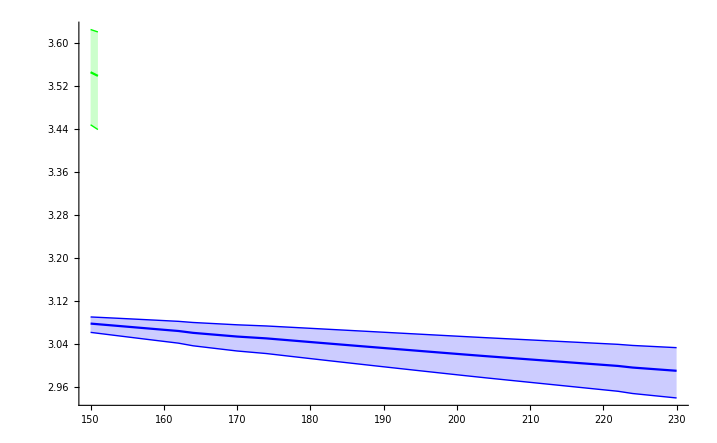

```mathematica
ListPlot[{Transpose[{Tscanc[[;;cc1Tmelt]],wrfitcc[[;;cc1Tmelt,1]]}],Transpose[{Tscanc[[;;cc1Tmelt]],wrfitccl[[;;cc1Tmelt,1]]}],Transpose[{Tscanc[[;;cc1Tmelt]],wrfitccu[[;;cc1Tmelt,1]]}],Transpose[{Tscanc[[;;cc2Tmelt]],wrfitcc[[;;cc2Tmelt,2]]}],Transpose[{Tscanc[[;;cc2Tmelt]],wrfitccl[[;;cc2Tmelt,2]]}],Transpose[{Tscanc[[;;cc2Tmelt]],wrfitccu[[;;cc2Tmelt,2]]}]},PlotRange->All,Filling->{1->{2},1->{3},4->{5},4->{6}},FillingStyle->Opacity[0.2],PlotStyle->{Blue,{Blue,Thin},{Blue,Thin},Green,{Green,Thin},{Green,Thin}},Joined->True]
```

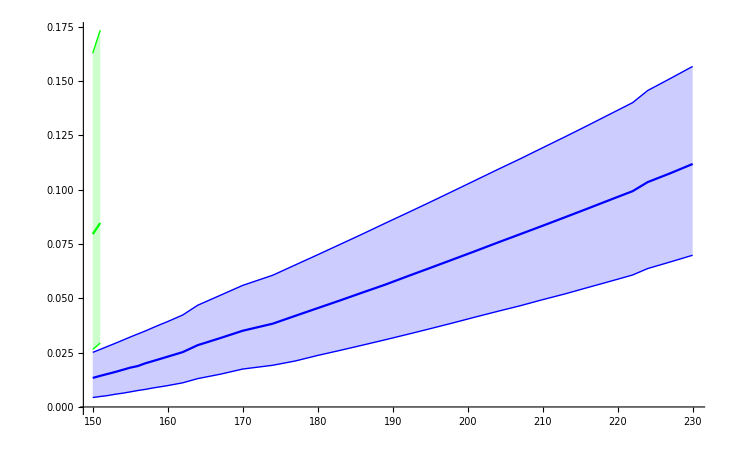

```mathematica
ListPlot[{Transpose[{Tscanc[[;;cc1Tmelt]],gfitcc[[;;cc1Tmelt,1]]}],Transpose[{Tscanc[[;;cc1Tmelt]],gfitccl[[;;cc1Tmelt,1]]}],Transpose[{Tscanc[[;;cc1Tmelt]],gfitccu[[;;cc1Tmelt,1]]}],Transpose[{Tscanc[[;;cc2Tmelt]],gfitcc[[;;cc2Tmelt,2]]}],Transpose[{Tscanc[[;;cc2Tmelt]],gfitccl[[;;cc2Tmelt,2]]}],Transpose[{Tscanc[[;;cc2Tmelt]],gfitccu[[;;cc2Tmelt,2]]}]},PlotRange->All,Filling->{1->{2},1->{3},4->{5},4->{6}},FillingStyle->Opacity[0.2],PlotStyle->{Blue,{Blue,Thin},{Blue,Thin},Green,{Green,Thin},{Green,Thin}},Joined->True]
```

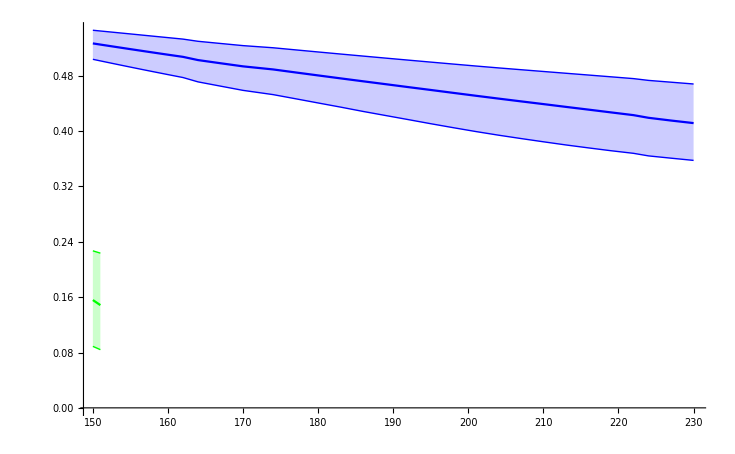

```mathematica
ListPlot[{Transpose[{Tscanc[[;;cc1Tmelt]],areafitcc[[;;cc1Tmelt,1]]}],Transpose[{Tscanc[[;;cc1Tmelt]],areafitccl[[;;cc1Tmelt,1]]}],Transpose[{Tscanc[[;;cc1Tmelt]],areafitccu[[;;cc1Tmelt,1]]}],Transpose[{Tscanc[[;;cc2Tmelt]],areafitcc[[;;cc2Tmelt,2]]}],Transpose[{Tscanc[[;;cc2Tmelt]],areafitccl[[;;cc2Tmelt,2]]}],Transpose[{Tscanc[[;;cc2Tmelt]],areafitccu[[;;cc2Tmelt,2]]}]},PlotRange->All,Filling->{1->{2},1->{3},4->{5},4->{6}},FillingStyle->Opacity[0.2],PlotStyle->{Blue,{Blue,Thin},{Blue,Thin},Green,{Green,Thin},{Green,Thin}},Joined->True]
```

## Charmonium Emission Rates

```mathematica
storefine[param_,res_,model_]:=Module[{temp=ToString[res]},res=Range[Length[model]];
Do[res[[i]]=Range[Length[model[[i]]]],{i,Length[model]}];Do[Do[res[[i,ii]]=param/.model[[i,ii]]["BestFitParameters"],{ii,Length[res[[i]]]}],{i,Length[res]}];Export["spectraldata/Tscan/cc/Tcfine/results/"<>temp<>".dat",res];];

storeareafine[res_,model_]:=Module[{temp=ToString[res]},res=Range[Length[model]];
Do[res[[i]]=Range[Length[model[[i]]]],{i,Length[model]}];Do[Do[res[[i,ii]]=π/2(Γ/.model[[i,ii]]["BestFitParameters"])( const/.model[[i,ii]]["BestFitParameters"]),{ii,Length[res[[i]]]}],{i,Length[res]}];Export["spectraldata/Tscan/cc/Tcfine/results/"<>temp<>".dat",res];];

importfine[res_]:=res=Import["spectraldata/Tscan/cc/Tcfine/results/"<>ToString[res]<>".dat"];
```

### Constant Chemical Potential

```mathematica
Emfactor=2.356447552594432;
nB[w_,T_]:=1/(Exp[w/T]-1);
```

```mathematica
R0=ConstantArray[0,cc1Tcut];
Do[R0[[ii]]={Tscanc[[ii]],Emfactor (areafitcc[[ii,2]]nB[wrfitcc[[ii,2]],Tscanc[[ii]]/1000])/(areafitcc[[ii,1]]nB[wrfitcc[[ii,1]],Tscanc[[ii]]/1000])},{ii,cc1Tcut}];
```

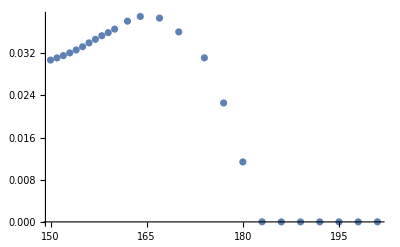

```mathematica
ListPlot[R0]
```

```mathematica
R0[[6]]
```

{155,0.0332409}

### Constant T = Tc

```mathematica
chemT={{0.,0.155},{0.01,0.155003},{0.02,0.15501},{0.03,0.155023},{0.04,0.15504},{0.05,0.155063},{0.06,0.15509},{0.07,0.155123},{0.08,0.155161},{0.09,0.155203},{0.1,0.155251},{0.11,0.155304},{0.12,0.155361},{0.13,0.155424},{0.14,0.155492},{0.15,0.155565},{0.16,0.155643},{0.17,0.155726},{0.18,0.155814},{0.19,0.155908},{0.2,0.156006},{0.21,0.15611},{0.22,0.156218},{0.23,0.156332},{0.24,0.156451},{0.25,0.156575},{0.26,0.156704},{0.27,0.156838},{0.28,0.156978},{0.29,0.157122},{0.3,0.157272},{0.31,0.157427},{0.32,0.157588},{0.33,0.157753},{0.34,0.157924},{0.35000000000000003,0.1581},{0.36,0.158282},{0.37,0.158468},{0.38,0.15866},{0.39,0.158858},{0.4,0.15906},{0.41000000000000003,0.159268},{0.42,0.159482},{0.43,0.1597},{0.44,0.159925},{0.45,0.160154},{0.46,0.160389},{0.47000000000000003,0.16063},{0.48,0.160876},{0.49,0.161127},{0.5,0.161384},{0.51,0.16164699999999999},{0.52,0.161915},{0.53,0.162188},{0.54,0.162468},{0.55,0.162752},{0.56,0.163043},{0.5700000000000001,0.163339},{0.58,0.163641},{0.59,0.163948},{0.6,0.164261},{0.61,0.16458},{0.62,0.164904},{0.63,0.165234},{0.64,0.16557},{0.65,0.165912},{0.66,0.166259},{0.67,0.166613},{0.68,0.166972},{0.6900000000000001,0.16733699999999999},{0.7000000000000001,0.167708},{0.71,0.168084},{0.72,0.168467},{0.73,0.168855},{0.74,0.16925},{0.75,0.16965},{0.76,0.17005599999999998},{0.77,0.170469},{0.78,0.170887},{0.79,0.171311},{0.8,0.171741},{0.81,0.172178},{0.8200000000000001,0.17262},{0.8300000000000001,0.173068},{0.84,0.17352299999999998},{0.85,0.173983},{0.86,0.17445},{0.87,0.174922},{0.88,0.175401},{0.89,0.175886},{0.9,0.176377},{0.91,0.176874},{0.92,0.177377},{0.93,0.177887},{0.9400000000000001,0.178403},{0.9500000000000001,0.178924},{0.96,0.179452},{0.97,0.179986},{0.98,0.180527},{0.99,0.18107299999999998},{1.,0.181626}};
chemTu={{0.,0.155},{0.01,0.155002},{0.02,0.155008},{0.03,0.155019},{0.04,0.155034},{0.05,0.155053},{0.06,0.155076},{0.07,0.155103},{0.08,0.155135},{0.09,0.155171},{0.1,0.155211},{0.11,0.155255},{0.12,0.155304},{0.13,0.155356},{0.14,0.155413},{0.15,0.155474},{0.16,0.15554},{0.17,0.15561},{0.18,0.155683},{0.19,0.155762},{0.2,0.155844},{0.21,0.155931},{0.22,0.156022},{0.23,0.156117},{0.24,0.156216},{0.25,0.15632},{0.26,0.156428},{0.27,0.15654099999999999},{0.28,0.156657},{0.29,0.156778},{0.3,0.156904},{0.31,0.157033},{0.32,0.157167},{0.33,0.157305},{0.34,0.157448},{0.35000000000000003,0.15759499999999999},{0.36,0.157746},{0.37,0.15790099999999999},{0.38,0.158061},{0.39,0.158226},{0.4,0.158394},{0.41000000000000003,0.158568},{0.42,0.158745},{0.43,0.15892699999999998},{0.44,0.159113},{0.45,0.159304},{0.46,0.159499},{0.47000000000000003,0.159699},{0.48,0.159903},{0.49,0.160111},{0.5,0.160324},{0.51,0.160542},{0.52,0.160764},{0.53,0.16099},{0.54,0.161221},{0.55,0.161456},{0.56,0.161696},{0.5700000000000001,0.161941},{0.58,0.162189},{0.59,0.162443},{0.6,0.16270099999999998},{0.61,0.162964},{0.62,0.163231},{0.63,0.163503},{0.64,0.163779},{0.65,0.16406},{0.66,0.164345},{0.67,0.164636},{0.68,0.16493},{0.6900000000000001,0.16523},{0.7000000000000001,0.165534},{0.71,0.165843},{0.72,0.166156},{0.73,0.166474},{0.74,0.166797},{0.75,0.167124},{0.76,0.167456},{0.77,0.167793},{0.78,0.168134},{0.79,0.168481},{0.8,0.168832},{0.81,0.169187},{0.8200000000000001,0.169548},{0.8300000000000001,0.169913},{0.84,0.170282},{0.85,0.170657},{0.86,0.171036},{0.87,0.171421},{0.88,0.171809},{0.89,0.172203},{0.9,0.172601},{0.91,0.173005},{0.92,0.17341299999999998},{0.93,0.173825},{0.9400000000000001,0.174243},{0.9500000000000001,0.174665},{0.96,0.175093},{0.97,0.175525},{0.98,0.175961},{0.99,0.176403},{1.,0.176849}};
chemTl={{0.,0.155},{0.01,0.155003},{0.02,0.155012},{0.03,0.155028},{0.04,0.15505},{0.05,0.155077},{0.06,0.155112},{0.07,0.155152},{0.08,0.155198},{0.09,0.155251},{0.1,0.15531},{0.11,0.15537499999999999},{0.12,0.155447},{0.13,0.155525},{0.14,0.155609},{0.15,0.155699},{0.16,0.155796},{0.17,0.155898},{0.18,0.156008},{0.19,0.156123},{0.2,0.156245},{0.21,0.156373},{0.22,0.156508},{0.23,0.156649},{0.24,0.156797},{0.25,0.156951},{0.26,0.157111},{0.27,0.157278},{0.28,0.157452},{0.29,0.157632},{0.3,0.15781799999999999},{0.31,0.158011},{0.32,0.158211},{0.33,0.158417},{0.34,0.158631},{0.35000000000000003,0.15885},{0.36,0.159077},{0.37,0.15931},{0.38,0.15955},{0.39,0.159797},{0.4,0.16005},{0.41000000000000003,0.160311},{0.42,0.160578},{0.43,0.160853},{0.44,0.161134},{0.45,0.161422},{0.46,0.161718},{0.47000000000000003,0.16202},{0.48,0.162329},{0.49,0.162646},{0.5,0.16297},{0.51,0.163301},{0.52,0.163639},{0.53,0.163984},{0.54,0.164337},{0.55,0.164697},{0.56,0.165064},{0.5700000000000001,0.165439},{0.58,0.165821},{0.59,0.166211},{0.6,0.166608},{0.61,0.167013},{0.62,0.167425},{0.63,0.167845},{0.64,0.168272},{0.65,0.168707},{0.66,0.16915},{0.67,0.169601},{0.68,0.170059},{0.6900000000000001,0.170525},{0.7000000000000001,0.170999},{0.71,0.171481},{0.72,0.17197099999999998},{0.73,0.172468},{0.74,0.172974},{0.75,0.173488},{0.76,0.174009},{0.77,0.174539},{0.78,0.175076},{0.79,0.175622},{0.8,0.176176},{0.81,0.176738},{0.8200000000000001,0.177308},{0.8300000000000001,0.177886},{0.84,0.178473},{0.85,0.179067},{0.86,0.17967},{0.87,0.180282},{0.88,0.180901},{0.89,0.181529},{0.9,0.182165},{0.91,0.18281},{0.92,0.183462},{0.93,0.184123},{0.9400000000000001,0.18479299999999999},{0.9500000000000001,0.185471},{0.96,0.186157},{0.97,0.186852},{0.98,0.187555},{0.99,0.188266},{1.,0.188986}};
```

```mathematica
Do[ccdataTc[n]=Import["spectraldata/Tscan/cc/Tcfine/swccT"<>ToString[Round[1000000 chemT[[All,2]]][[n]]]<>"spectra.dat"];,{n,Length[chemT]}];
{{Do[ccdataTcu[n]=Import["spectraldata/Tscan/cc/Tcfine/swccT"<>ToString[Round[1000000chemTu[[All,2]]][[n]]]<>"uspectra.dat"];,{n,Length[chemTu]}];}, {Do[ccdataTcl[n]=Import["spectraldata/Tscan/cc/Tcfine/swccT"<>ToString[Round[1000000 chemTl[[All,2]]][[n]]]<>"lspectra.dat"];,{n,Length[chemTl]}];}}
(*Manipulate[ListPlot[ccdataTc[n],Joined->True],{n,1,Length[chemT],1}]*)
```

{{Null},{Null}}

```mathematica
Clear[ccmodelTc,ccmodelTcl,ccmodelTcu]
fitnew[ccdataTc,ccmodelTc,chemT[[All,2]]];
fitnew[ccdataTcu,ccmodelTcu,chemTu[[All,2]]];
fitnew[ccdataTcl,ccmodelTcl,chemTl[[All,2]]];
```

```mathematica
Do[If[Length[ccmodelTc[[i]]]>2,ccmodelTc[[i]]=ccmodelTc[[i,;;2]]];,{i,Length[ccmodelTc]}];
Do[If[Length[ccmodelTcu[[i]]]>2,ccmodelTcu[[i]]=ccmodelTcu[[i,;;2]]];,{i,Length[ccmodelTcu]}];
Do[If[Length[ccmodelTcl[[i]]]>2,ccmodelTcl[[i]]=ccmodelTcl[[i,;;2]]];,{i,Length[ccmodelTcl]}];
```

```mathematica
Clear[Tcwrfitcc,Tcgfitcc,Tcareafitcc,Tccfitcc,Tcdfitcc,Tcsfitcc,Tcs2fitcc,Tcwrfitccu,Tcgfitccu,Tcareafitccu,Tccfitccu,Tcdfitccu,Tcsfitccu,Tcs2fitccu,Tcwrfitccl,Tcgfitccl,Tcareafitccl,Tccfitccl,Tcdfitccl,Tcsfitccl,Tcs2fitccl];
storefine[wr,Tcwrfitcc,ccmodelTc];
storefine[Γ,Tcgfitcc,ccmodelTc];
storefine[const,Tccfitcc,ccmodelTc];
storefine[δbg,Tcdfitcc,ccmodelTc];
storefine[shift,Tcsfitcc,ccmodelTc];
storefine[shift2,Tcs2fitcc,ccmodelTc];
storeareafine[Tcareafitcc,ccmodelTc];
storefine[wr,Tcwrfitccu,ccmodelTcu];
storefine[Γ,Tcgfitccu,ccmodelTcu];
storefine[const,Tccfitccu,ccmodelTcu];
storefine[δbg,Tcdfitccu,ccmodelTcu];
storefine[shift,Tcsfitccu,ccmodelTcu];
storefine[shift2,Tcs2fitccu,ccmodelTcu];
storeareafine[Tcareafitccu,ccmodelTcu];
storefine[wr,Tcwrfitccl,ccmodelTcl];
storefine[Γ,Tcgfitccl,ccmodelTcl];
storefine[const,Tccfitccl,ccmodelTcl];
storefine[δbg,Tcdfitccl,ccmodelTcl];
storefine[shift,Tcsfitccl,ccmodelTcl];
storefine[shift2,Tcs2fitccl,ccmodelTcl];
storeareafine[Tcareafitccl,ccmodelTcl];
```

```mathematica
importfine[Tcwrfitcc];
importfine[Tcgfitcc];
importfine[Tccfitcc];
importfine[Tcdfitcc];
importfine[Tcsfitcc];
importfine[Tcs2fitcc];
importfine[Tcareafitcc];
importfine[Tcwrfitccu];
importfine[Tcgfitccu];
importfine[Tccfitccu];
importfine[Tcdfitccu];
importfine[Tcsfitccu];
importfine[Tcs2fitccu];
importfine[Tcareafitccu];
importfine[Tcwrfitccl];
importfine[Tcgfitccl];
importfine[Tccfitccl];
importfine[Tcdfitccl];
importfine[Tcsfitccl];
importfine[Tcs2fitccl];
importfine[Tcareafitccl];
```

```mathematica
Manipulate[Show[{ListPlot[ccdataTc[i],Joined->True],Plot[BW[x,Tcwrfitcc[[i,ii]],Tcgfitcc[[i,ii]],Tcdfitcc[[i,ii]],Tccfitcc[[i,ii]],Tcsfitcc[[i,ii]],Tcs2fitcc[[i,ii]]],{x,0.7Tcwrfitcc[[i,ii]],1.3Tcwrfitcc[[i,ii]]},PlotStyle->{Red,Dashed},PlotRange->All],Plot[BWi[x,Tcwrfitcc[[i,ii]],Tcgfitcc[[i,ii]],Tccfitcc[[i,ii]]],{x,0.7Tcwrfitcc[[i,ii]],1.3Tcwrfitcc[[i,ii]]},PlotStyle->{Green,Dashed},PlotRange->All]}],{i,1,Length[Tcwrfitcc],1},{ii,1,Length[Tcwrfitcc[[1]]],1}]
```

ListPlot::lpn: ccdataTc[1.] is not a list of numbers or pairs of numbers.

Part::partd: Part specification Tcwrfitcc⟦1,1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Plot::plln: Limiting value 0.7 Tcwrfitcc⟦1,1⟧ in {x,0.7 Tcwrfitcc⟦1,1⟧,1.3 Tcwrfitcc⟦1,1⟧} is not a machine-sized real number.

Show::gcomb: Could not combine the graphics objects in Show[{ListPlot[ccdataTc[1],Joined→True],Plot[BW[x,Tcwrfitcc⟦FE`i$$32,FE`ii$$32⟧,Tcgfitcc⟦FE`i$$32,FE`ii$$32⟧,Tcdfitcc⟦FE`i$$32,FE`ii$$32⟧,Tccfitcc⟦FE`i$$32,FE`ii$$32⟧,Tcsfitcc⟦FE`i$$32,FE`ii$$32⟧,Tcs2fitcc⟦FE`i$$32,FE`ii$$32⟧],{x,0.7 Tcwrfitcc⟦FE`i$$32,FE`ii$$32⟧,1.3 Tcwrfitcc⟦FE`i$$32,FE`ii$$32⟧},PlotStyle→{Red,Dashed},PlotRange→All],Plot[BWi[x,Tcwrfitcc⟦FE`i$$32,FE`ii$$32⟧,Tcgfitcc⟦FE`i$$32,FE`ii$$32⟧,Tccfitcc⟦FE`i$$32,FE`ii$$32⟧],{x,0.7 Tcwrfitcc⟦FE`i$$32,FE`ii$$32⟧,1.3 Tcwrfitcc⟦FE`i$$32,FE`ii$$32⟧},PlotStyle→{Green,Dashed},PlotRange→All]}].

Plot::plln: Limiting value 0.7 Tcwrfitcc⟦1,1⟧ in {x,0.7 Tcwrfitcc⟦1,1⟧,1.3 Tcwrfitcc⟦1,1⟧} is not a machine-sized real number.

General::stop: Further output of Plot::plln will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in Show[{ListPlot[ccdataTc[1],Joined→True],Plot[BW[x,Tcwrfitcc⟦FE`i$$32,FE`ii$$32⟧,Tcgfitcc⟦FE`i$$32,FE`ii$$32⟧,Tcdfitcc⟦FE`i$$32,FE`ii$$32⟧,Tccfitcc⟦FE`i$$32,FE`ii$$32⟧,Tcsfitcc⟦FE`i$$32,FE`ii$$32⟧,Tcs2fitcc⟦FE`i$$32,FE`ii$$32⟧],{x,0.7 Tcwrfitcc⟦FE`i$$32,FE`ii$$32⟧,1.3 Tcwrfitcc⟦FE`i$$32,FE`ii$$32⟧},PlotStyle→{Red,Dashed},PlotRange→All],Plot[BWi[x,Tcwrfitcc⟦FE`i$$32,FE`ii$$32⟧,Tcgfitcc⟦FE`i$$32,FE`ii$$32⟧,Tccfitcc⟦FE`i$$32,FE`ii$$32⟧],{x,0.7 Tcwrfitcc⟦FE`i$$32,FE`ii$$32⟧,1.3 Tcwrfitcc⟦FE`i$$32,FE`ii$$32⟧},PlotStyle→{Green,Dashed},PlotRange→All]}].

```mathematica
Manipulate[Show[{ListPlot[ccdataTcl[i],Joined->True],Plot[BW[x,Tcwrfitccl[[i,ii]],Tcgfitccl[[i,ii]],Tcdfitccl[[i,ii]],Tccfitccl[[i,ii]],Tcsfitccl[[i,ii]],Tcs2fitccl[[i,ii]]],{x,0.7Tcwrfitccl[[i,ii]],1.3Tcwrfitccl[[i,ii]]},PlotStyle->{Red,Dashed},PlotRange->All],Plot[BWi[x,Tcwrfitccl[[i,ii]],Tcgfitccl[[i,ii]],Tccfitccl[[i,ii]]],{x,0.7Tcwrfitccl[[i,ii]],1.3Tcwrfitccl[[i,ii]]},PlotStyle->{Green,Dashed},PlotRange->All]}],{i,1,Length[Tcwrfitccl],1},{ii,1,Length[Tcwrfitccl[[1]]],1}]
```

ListPlot::lpn: ccdataTcl[1.] is not a list of numbers or pairs of numbers.

Part::partd: Part specification Tcwrfitccl⟦1,1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Plot::plln: Limiting value 0.7 Tcwrfitccl⟦1,1⟧ in {x,0.7 Tcwrfitccl⟦1,1⟧,1.3 Tcwrfitccl⟦1,1⟧} is not a machine-sized real number.

Show::gcomb: Could not combine the graphics objects in Show[{ListPlot[ccdataTcl[1],Joined→True],Plot[BW[x,Tcwrfitccl⟦FE`i$$35,FE`ii$$35⟧,Tcgfitccl⟦FE`i$$35,FE`ii$$35⟧,Tcdfitccl⟦FE`i$$35,FE`ii$$35⟧,Tccfitccl⟦FE`i$$35,FE`ii$$35⟧,Tcsfitccl⟦FE`i$$35,FE`ii$$35⟧,Tcs2fitccl⟦FE`i$$35,FE`ii$$35⟧],{x,0.7 Tcwrfitccl⟦FE`i$$35,FE`ii$$35⟧,1.3 Tcwrfitccl⟦FE`i$$35,FE`ii$$35⟧},PlotStyle→{Red,Dashed},PlotRange→All],Plot[BWi[x,Tcwrfitccl⟦FE`i$$35,FE`ii$$35⟧,Tcgfitccl⟦FE`i$$35,FE`ii$$35⟧,Tccfitccl⟦FE`i$$35,FE`ii$$35⟧],{x,0.7 Tcwrfitccl⟦FE`i$$35,FE`ii$$35⟧,1.3 Tcwrfitccl⟦FE`i$$35,FE`ii$$35⟧},PlotStyle→{Green,Dashed},PlotRange→All]}].

Plot::plln: Limiting value 0.7 Tcwrfitccl⟦1,1⟧ in {x,0.7 Tcwrfitccl⟦1,1⟧,1.3 Tcwrfitccl⟦1,1⟧} is not a machine-sized real number.

General::stop: Further output of Plot::plln will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in Show[{ListPlot[ccdataTcl[1],Joined→True],Plot[BW[x,Tcwrfitccl⟦FE`i$$35,FE`ii$$35⟧,Tcgfitccl⟦FE`i$$35,FE`ii$$35⟧,Tcdfitccl⟦FE`i$$35,FE`ii$$35⟧,Tccfitccl⟦FE`i$$35,FE`ii$$35⟧,Tcsfitccl⟦FE`i$$35,FE`ii$$35⟧,Tcs2fitccl⟦FE`i$$35,FE`ii$$35⟧],{x,0.7 Tcwrfitccl⟦FE`i$$35,FE`ii$$35⟧,1.3 Tcwrfitccl⟦FE`i$$35,FE`ii$$35⟧},PlotStyle→{Red,Dashed},PlotRange→All],Plot[BWi[x,Tcwrfitccl⟦FE`i$$35,FE`ii$$35⟧,Tcgfitccl⟦FE`i$$35,FE`ii$$35⟧,Tccfitccl⟦FE`i$$35,FE`ii$$35⟧],{x,0.7 Tcwrfitccl⟦FE`i$$35,FE`ii$$35⟧,1.3 Tcwrfitccl⟦FE`i$$35,FE`ii$$35⟧},PlotStyle→{Green,Dashed},PlotRange→All]}].

```mathematica
R0Tc=ConstantArray[0,Length[Tcwrfitcc]];
Do[R0Tc[[ii]]={chemT[[ii,1]],Emfactor (Tcareafitcc[[ii,2]]nB[Tcwrfitcc[[ii,2]],chemT[[ii,2]]])/(Tcareafitcc[[ii,1]]nB[Tcwrfitcc[[ii,1]],chemT[[ii,2]]])},{ii,Length[R0Tc]}];
R0Tcu=ConstantArray[0,Length[Tcwrfitccu]];
Do[R0Tcu[[ii]]={chemTu[[ii,1]],Emfactor (Tcareafitccu[[ii,2]]nB[Tcwrfitccu[[ii,2]],chemTu[[ii,2]]])/(Tcareafitccu[[ii,1]]nB[Tcwrfitccu[[ii,1]],chemTu[[ii,2]]])},{ii,Length[R0Tcu]}];
R0Tcl=ConstantArray[0,Length[Tcwrfitccl]];
Do[R0Tcl[[ii]]={chemTl[[ii,1]],Emfactor (Tcareafitccl[[ii,2]]nB[Tcwrfitccl[[ii,2]],chemTl[[ii,2]]])/(Tcareafitccl[[ii,1]]nB[Tcwrfitccl[[ii,1]],chemTl[[ii,2]]])},{ii,Length[R0Tcl]}];
```

Part::partw: Part 2 of {0.486477} does not exist.

Part::partw: Part 2 of {3.04803} does not exist.

```mathematica
R0Tcu=Delete[R0Tcu,37]
```

{{0.,0.0299417},{0.01,0.0299301},{0.02,0.0299577},{0.03,0.0299089},{0.04,0.029832},{0.05,0.0298026},{0.06,0.0298458},{0.07,0.0297282},{0.08,0.0297358},{0.09,0.0296937},{0.1,0.0296469},{0.11,0.0295149},{0.12,0.0294782},{0.13,0.029471},{0.14,0.0293101},{0.15,0.0292788},{0.16,0.0290519},{0.17,0.0289686},{0.18,0.0288585},{0.19,0.0287505},{0.2,0.0285818},{0.21,0.0284068},{0.22,0.0281939},{0.23,0.0279928},{0.24,0.0278597},{0.25,0.0275891},{0.26,0.0273459},{0.27,0.0271045},{0.28,0.0267697},{0.29,0.0265153},{0.3,0.0261686},{0.31,0.0258533},{0.32,0.0254508},{0.33,0.0249985},{0.34,0.0247298},{0.35,0.0241871},{0.37,0.0232794},{0.38,0.0226972},{0.39,0.0222001},{0.4,0.0217136},{0.41,0.0210519},{0.42,0.0203721},{0.43,0.0197353},{0.44,0.0190684},{0.45,0.0182125},{0.46,0.0175468},{0.47,0.0165624},{0.48,0.0156718},{0.49,0.014801},{0.5,0.0138437},{0.51,0.0128735},{0.52,0.0116073},{0.53,0.0104708},{0.54,0.0093956},{0.55,0.00813262},{0.56,0.00701749},{0.57,0.005692},{0.58,0.00421326},{0.59,0.00274179},{0.6,0.00151121},{0.61,0.000109369},{0.62,0.0000183103},{0.63,9.61175×10^-6},{0.64,6.20364×10^-6},{0.65,5.30929×10^-6},{0.66,4.19895×10^-6},{0.67,3.78894×10^-6},{0.68,3.17202×10^-6},{0.69,2.92496×10^-6},{0.7,2.70373×10^-6},{0.71,2.53086×10^-6},{0.72,2.36217×10^-6},{0.73,2.17016×10^-6},{0.74,2.19935×10^-6},{0.75,2.05944×10^-6},{0.76,2.12124×10^-6},{0.77,2.22086×10^-6},{0.78,2.27974×10^-6},{0.79,2.36213×10^-6},{0.8,2.40077×10^-6},{0.81,2.56806×10^-6},{0.82,2.62504×10^-6},{0.83,2.73636×10^-6},{0.84,2.77386×10^-6},{0.85,2.96501×10^-6},{0.86,3.10487×10^-6},{0.87,3.29529×10^-6},{0.88,3.50555×10^-6},{0.89,3.63758×10^-6},{0.9,3.93575×10^-6},{0.91,4.10959×10^-6},{0.92,4.4076×10^-6},{0.93,4.74773×10^-6},{0.94,4.97461×10^-6},{0.95,5.49088×10^-6},{0.96,5.68307×10^-6},{0.97,6.02035×10^-6},{0.98,6.30701×10^-6},{0.99,6.97928×10^-6},{1.,7.5753×10^-6}}

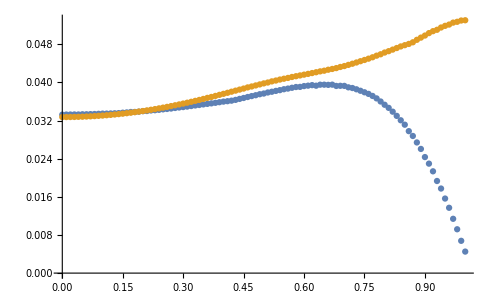

```mathematica
ListPlot[{R0Tc,R0Tcl}]
```

## Bottomonium

```mathematica
Tscanb=IntegerPart[1000 Table[i,{i,0.15,0.6,0.005}]]
```

{150,155,160,164,169,175,180,185,190,195,200,205,210,215,220,224,229,235,240,245,250,255,260,265,270,275,280,285,290,295,300,305,310,315,320,325,329,334,339,345,350,355,360,365,370,375,380,385,390,395,400,405,410,415,420,425,430,435,439,444,449,454,459,464,470,475,480,485,490,495,500,505,510,515,520,525,530,535,540,545,550,555,560,565,570,575,580,585,590,595,600}

```mathematica
Do[bbdata[n]=Import["spectraldata/Tscan/bb/swbbT"<>ToString[Tscanb[[n]]]<>"spectra.dat"];,{n,Length[Tscanb]}];
Manipulate[ListPlot[bbdata[n],Joined->True],{n,1,Length[Tscanb],1}]
```

ListPlot::lpn: bbdata[1.] is not a list of numbers or pairs of numbers.

```mathematica
Do[bbdatal[n]=Import["spectraldata/Tscan/bb/swbbT"<>ToString[Tscanb[[n]]]<>"lspectra.dat"];,{n,Length[Tscanb]}];
Manipulate[ListPlot[bbdatal[n],Joined->True],{n,1,Length[Tscanb],1}]
```

ListPlot::lpn: bbdatal[1.] is not a list of numbers or pairs of numbers.

```mathematica
Do[bbdatau[n]=Import["spectraldata/Tscan/bb/swbbT"<>ToString[Tscanb[[n]]]<>"uspectra.dat"];,{n,Length[Tscanb]}];
Manipulate[ListPlot[bbdatau[n],Joined->True],{n,1,Length[Tscanb],1}]
```

ListPlot::lpn: bbdatau[1.] is not a list of numbers or pairs of numbers.

### Fitting

```mathematica
Clear[bbmodel,bbmodelu,bbmodell]
fitnew[bbdata,bbmodel,Tscanb];
fitnew[bbdatau,bbmodelu,Tscanb];
fitnew[bbdatal,bbmodell,Tscanb];
```

### Store Results

```mathematica
Do[If[Length[bbmodel[[i]]]>4,bbmodel[[i]]=bbmodel[[i,;;4]]];If[Length[bbmodelu[[i]]]>4,bbmodelu[[i]]=bbmodelu[[i,;;4]]];If[Length[bbmodell[[i]]]>4,bbmodell[[i]]=bbmodell[[i,;;4]]];,{i,Length[bbmodel]}];
```

```mathematica
Clear[wrfitbb,wrfitbbl,wrfitbbu,gfitbb,gfitbbl,gfitbbu,areafitbb,areafitbbu,areafitbbl,cfitbb,cfitbbl,cfitbbu,dfitbb,dfitbbl,dfitbbu,sfitbb,sfitbbl,sfitbbu,s2fitbb,s2fitbbl,s2fitbbu];
store[wr,wrfitbb,bbmodel];
store[wr,wrfitbbl,bbmodell];
store[wr,wrfitbbu,bbmodelu];
store[Γ,gfitbb,bbmodel];
store[Γ,gfitbbl,bbmodell];
store[Γ,gfitbbu,bbmodelu];
store[const,cfitbb,bbmodel];
store[const,cfitbbl,bbmodell];
store[const,cfitbbu,bbmodelu];
store[δbg,dfitbb,bbmodel];
store[δbg,dfitbbl,bbmodell];
store[δbg,dfitbbu,bbmodelu];
store[shift,sfitbb,bbmodel];
store[shift,sfitbbl,bbmodell];
store[shift,sfitbbu,bbmodelu];
store[shift2,s2fitbb,bbmodel];
store[shift2,s2fitbbl,bbmodell];
store[shift2,s2fitbbu,bbmodelu];
storearea[areafitbb,bbmodel];
storearea[areafitbbl,bbmodell];
storearea[areafitbbu,bbmodelu];
```

### Display Results

```mathematica
import[wrfitbb];
import[wrfitbbl];
import[wrfitbbu];
import[gfitbb];
import[gfitbbl];
import[gfitbbu];
import[cfitbb];
import[cfitbbl];
import[cfitbbu];
import[dfitbb];
import[dfitbbl];
import[dfitbbu];
import[sfitbb];
import[sfitbbl];
import[sfitbbu];
import[s2fitbb];
import[s2fitbbl];
import[s2fitbbu];
import[areafitbb];
import[areafitbbl];
import[areafitbbu];
```

```mathematica
Do[If[Length[wrfitbb[[-i]]]<2,bb1Tcut=Length[wrfitbb]-i];,{i,Length[wrfitbb]}];
Do[If[Length[wrfitbbu[[-i]]]<2,bb1uTcut=Length[wrfitbbu]-i];,{i,Length[wrfitbbu]}];
Do[If[Length[wrfitbbl[[-i]]]<2,bb1lTcut=Length[wrfitbbl]-i];,{i,Length[wrfitbbl]}];
Do[If[Length[wrfitbb[[-i]]]<3,bb2Tcut=Length[wrfitbb]-i];,{i,Length[wrfitbb]}];
Do[If[Length[wrfitbbu[[-i]]]<3,bb2uTcut=Length[wrfitbbu]-i];,{i,Length[wrfitbbu]}];
Do[If[Length[wrfitbbl[[-i]]]<3,bb2lTcut=Length[wrfitbbl]-i];,{i,Length[wrfitbbl]}];
Do[If[Length[wrfitbb[[-i]]]<4,bb3Tcut=Length[wrfitbb]-i];,{i,Length[wrfitbb]}];Do[If[Length[wrfitbbu[[-i]]]<4,bb3uTcut=Length[wrfitbbu]-i];,{i,Length[wrfitbbu]}];Do[If[Length[wrfitbbl[[-i]]]<4,bb3lTcut=Length[wrfitbbl]-i];,{i,Length[wrfitbbl]}];
```

```mathematica
Manipulate[Show[{ListPlot[bbdata[i],Joined->True],Plot[BW[x,wrfitbb[[i,ii]],gfitbb[[i,ii]],dfitbb[[i,ii]],cfitbb[[i,ii]],sfitbb[[i,ii]],s2fitbb[[i,ii]]],{x,0.7wrfitbb[[i,ii]],1.3wrfitbb[[i,ii]]},PlotStyle->{Red,Dashed},PlotRange->All],Plot[BWi[x,wrfitbb[[i,ii]],gfitbb[[i,ii]],cfitbb[[i,ii]]],{x,0.7wrfitbb[[i,ii]],1.3wrfitbb[[i,ii]]},PlotStyle->{Green,Dashed},PlotRange->All]}],{i,1,Length[wrfitbb],1},{ii,1,Length[wrfitbb[[1]]],1}]
```

```mathematica
bbcont={10.47459661653534,10.386991291819312,10.320189935556595,10.266520483724824,10.221771783701307,10.183415247448838,10.14982884042086,10.119917801704643,10.092912804537864,10.068255145767312,10.045527844650223,10.024869142170065,10.00606442137611,9.988248930352256,9.971300912748175,9.955119189686751,9.939618860084348,9.924728047184722,9.91038541425775,9.896538234463003,9.883140878360269,9.870153615237932,9.857541654132588,9.84527436973816,9.833324672428462,9.821668491664653,9.810284349405235,9.799153005449387,9.788257160460661,9.777581207953114,9.76711102016143,9.756833770672042,9.746737782242517,9.736812392434949,9.727047840979282,9.717435173901784,9.7079661552598,9.698633193697498,9.68942927922979,9.680347923072885,9.67138310961781,9.662529251650565,9.653781149410847,9.645133958371117,9.636583155264336,9.628124512339577,9.61975407153492,9.611468121959486,9.603263180915544,9.595135974071855,9.587083421208572,9.579102619219741,9.571190830899964,9.563345470697755,9.555564095574915,9.547844393123798,9.540184174031799,9.53258136207098,9.525033987912632,9.517540180573716,9.510098162358636,9.502706241507756,9.495362807980896,9.488066327240787,9.48081533651431,9.473608439770503,9.466444304106242,9.459321655963414,9.452239277450436,9.445196003567682,9.438190718761756,9.431222354618207,9.424289886819881,9.41739233320969,9.41052875109574,9.403698235563585,9.396899917176915,9.390132960386843,9.38339656168247,9.376689947990425,9.370012375266969,9.36336312688355,9.35674151254152,9.350146866770242,9.343578547940272,9.33703593705241,9.330518436688472,9.324025470075904,9.317556480121242,9.311110928532827,9.30468829499006};
```

```mathematica
bbcontl={10.874752316247209,10.709348069405426,10.596996983853511,10.513609526664556,10.448050062654799,10.394377961943272,10.349100389805146,10.310013199330372,10.275648390839436,10.244985723301182,10.217291240093466,10.192656427134342,10.17070083709334,10.150179417217462,10.130898694948609,10.112700563371412,10.09545434620659,10.079050929257686,10.06339836626425,10.048418528941538,10.034044525430874,10.020218685932695,10.00689097404341,9.994017721286706,9.98156060985683,9.969485847976985,9.957763496194124,9.946366912891172,9.935272294413215,9.924458294065756,9.913905696702223,9.90359715051309,9.893516938772313,9.883650780248214,9.873985662596134,9.864509701325682,9.855212011249385,9.846082599813219,9.837112275769512,9.828292562976062,9.81961563171522,9.811074235092388,9.802661651139303,9.794371637465265,9.786198383598345,9.778136475103457,9.770180857650889,9.762326805812604,9.754569896973951,9.746905983922625,9.739331175545635,9.731841813362315,9.724434456566103,9.717105862390124,9.709852974075199,9.702672904521538,9.695562926502934,9.68852045889942,9.68154305879914,9.674628409712207,9.66777431524974,9.660978688961679,9.654239549172559,9.647555010387574,9.640923278713544,9.634342644998762,9.62781148025183,9.621328230674246,9.614891412742095,9.608499609808543,9.602151467377281,9.5958456903678,9.589581038903399,9.583356326100771,9.577170414297424,9.57102221316282,9.56491067649701,9.558834800375598,9.552793620679699,9.546786211051996,9.54081168120238,9.534869174654393,9.528957867624023,9.523076966842094,9.517225708521403,9.51140335671006,9.50560920195353,9.499842560187231,9.494102771471903,9.48838919889178,9.482701227510523};
```

```mathematica
bbcontu={10.27542190323936,10.210306841307867,10.15813391734028,10.11462599593822,10.077265424837341,10.044459777661434,10.015145362901704,9.98858052848785,9.964229937359468,9.941695968597415,9.9206761123795,9.901314731636493,9.883457006803193,9.866397905341865,9.850044414651597,9.834318525972737,9.819154228885557,9.80449520814989,9.790293066036469,9.776505926422514,9.763097330640862,9.750035354706515,9.737291897306735,9.724842100702306,9.712663876105138,9.700737511905654,9.68904534815287,9.677571504347467,9.666301650244467,9.65522281351977,9.644323212761897,9.633592118643751,9.623019734229503,9.612597088822872,9.602315948680184,9.592168740676637,9.58214848184051,9.57224872049114,9.562463485331138,9.55278723703638,9.543214829303091,9.53374147251674,9.524362700565154,9.515074344335435,9.505872504173217,9.49675352858603,9.487713993107569,9.478750681784883,9.46986057136048,9.461040815122214,9.45228873076509,9.443601786640313,9.434977592036402,9.426413885695805,9.417908527788732,9.409459490359788,9.401064850625268,9.392722782960972,9.38443155330194,9.376189512350782,9.367995090888918,9.35984679399565,9.351743197060335,9.343682940911478,9.335664728303266,9.327687319912036,9.31974953110982,9.311850228764314,9.303988328216592,9.29616279070657,9.288372620665468,9.28061686349764,9.272894603234423,9.265204960598545,9.25754709096879,9.249920182665566,9.242323455202108,9.234756157743245,9.22721756760527,9.219706988873012,9.212223751090171,9.204767208043139,9.19733673658531,9.189931735582011,9.182551624856343,9.17519584424124,9.167863852678373,9.160555127338563,9.153269162822552,9.146005470394678,9.138763577258592};
```

```mathematica
bbbind=bbcont-wrfitbb;
bbbindu=bbcontu-wrfitbbu;
bbbindl=bbcontl-wrfitbbl;
```

```mathematica
Do[If[(bbbind-gfitbb)[[i,1]]>0,bb1Tmelt=i],{i,1,Length[bbbind]}];
Do[If[(bbbind-gfitbb)[[i,2]]>0,bb2Tmelt=i],{i,1,bb1Tcut}];
Do[If[(bbbind-gfitbb)[[i,3]]>0,bb3Tmelt=i],{i,1,bb2Tcut}];
Do[If[(bbbind-gfitbb)[[i,4]]>0,bb4Tmelt=i,bb4Tmelt=1],{i,1,bb3Tcut}];
```

```mathematica
Do[If[(bbbindu-gfitbbu)[[i,1]]>0,bb1uTmelt=i],{i,1,Length[bbbind]}];
Do[If[(bbbindu-gfitbbu)[[i,2]]>0,bb2uTmelt=i],{i,1,bb1uTcut}];
Do[If[(bbbindu-gfitbbu)[[i,3]]>0,bb3uTmelt=i,bb3uTmelt=1],{i,1,bb2uTcut}];
Do[If[(bbbindu-gfitbbu)[[i,4]]>0,bb4uTmelt=i,bb4uTmelt=1],{i,1,bb3uTcut}];
```

```mathematica
Do[If[(bbbindl-gfitbbl)[[i,1]]>0,bb1lTmelt=i+1],{i,1,Length[bbbind]}];
Do[If[(bbbindl-gfitbbl)[[i,2]]>0,bb2lTmelt=i+1],{i,1,bb1lTcut}];
Do[If[(bbbindl-gfitbbl)[[i,3]]>0,bb3lTmelt=i+1],{i,1,bb2lTcut}];
Do[If[(bbbindl-gfitbbl)[[i,4]]>0,bb4lTmelt=i+1],{i,1,bb3lTcut}];
```

```mathematica
N[{Tscanb[[bb1lTmelt]],Tscanb[[bb1Tmelt]],Tscanb[[bb1uTmelt]]}/155]
```

{3.70968,3.03226,2.58065}

```mathematica
N[{Tscanb[[bb2lTmelt]],Tscanb[[bb2Tmelt]],Tscanb[[bb2uTmelt]]}/155]
```

{1.6129,1.32258,1.16129}

```mathematica
N[{Tscanb[[bb3lTmelt]],Tscanb[[bb3Tmelt]],Tscanb[[bb3uTmelt]]}/155]
```

{1.19355,1.03226,0.967742}

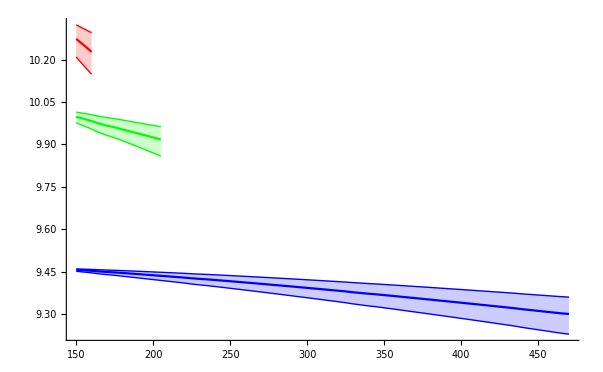

```mathematica
ListPlot[{Transpose[{Tscanb[[;;bb1Tmelt]],wrfitbb[[;;bb1Tmelt,1]]}],Transpose[{Tscanb[[;;bb1Tmelt]],wrfitbbl[[;;bb1Tmelt,1]]}],Transpose[{Tscanb[[;;bb1Tmelt]],wrfitbbu[[;;bb1Tmelt,1]]}],Transpose[{Tscanb[[;;bb2Tmelt]],wrfitbb[[;;bb2Tmelt,2]]}],Transpose[{Tscanb[[;;bb2Tmelt]],wrfitbbl[[;;bb2Tmelt,2]]}],Transpose[{Tscanb[[;;bb2Tmelt]],wrfitbbu[[;;bb2Tmelt,2]]}],Transpose[{Tscanb[[;;bb3Tmelt]],wrfitbb[[;;bb3Tmelt,3]]}],Transpose[{Tscanb[[;;bb3Tmelt]],wrfitbbl[[;;bb3Tmelt,3]]}],Transpose[{Tscanb[[;;bb3Tmelt]],wrfitbbu[[;;bb3Tmelt,3]]}]},PlotRange->All,Filling->{1->{2},1->{3},4->{5},4->{6},7->{8},7->{9}},FillingStyle->Opacity[0.2],PlotStyle->{Blue,{Blue,Thin},{Blue,Thin},Green,{Green,Thin},{Green,Thin},Red,{Red,Thin},{Red,Thin}},Joined->True]
```

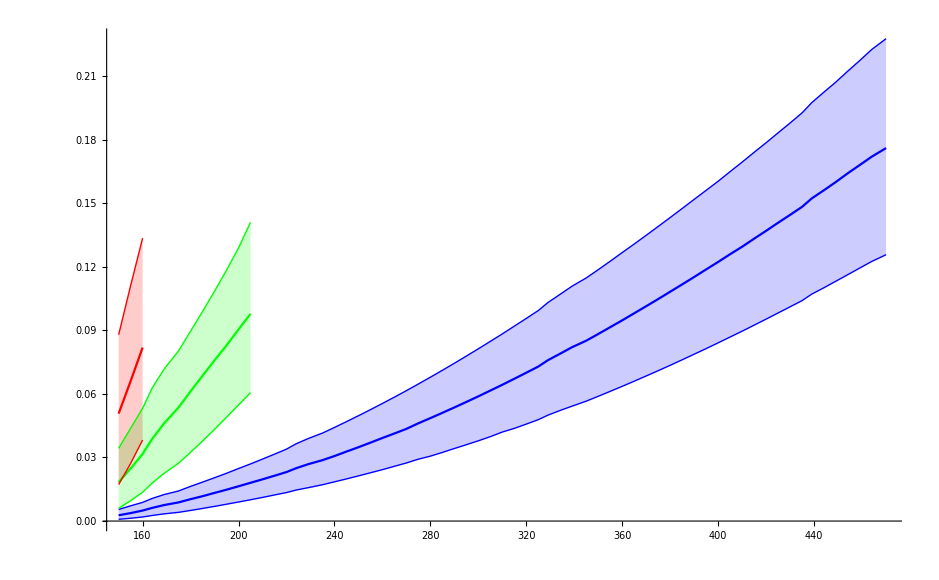

```mathematica
ListPlot[{Transpose[{Tscanb[[;;bb1Tmelt]],gfitbb[[;;bb1Tmelt,1]]}],Transpose[{Tscanb[[;;bb1Tmelt]],gfitbbl[[;;bb1Tmelt,1]]}],Transpose[{Tscanb[[;;bb1Tmelt]],gfitbbu[[;;bb1Tmelt,1]]}],Transpose[{Tscanb[[;;bb2Tmelt]],gfitbb[[;;bb2Tmelt,2]]}],Transpose[{Tscanb[[;;bb2Tmelt]],gfitbbl[[;;bb2Tmelt,2]]}],Transpose[{Tscanb[[;;bb2Tmelt]],gfitbbu[[;;bb2Tmelt,2]]}],Transpose[{Tscanb[[;;bb3Tmelt]],gfitbb[[;;bb3Tmelt,3]]}],Transpose[{Tscanb[[;;bb3Tmelt]],gfitbbl[[;;bb3Tmelt,3]]}],Transpose[{Tscanb[[;;bb3Tmelt]],gfitbbu[[;;bb3Tmelt,3]]}]},PlotRange->All,Filling->{1->{2},1->{3},4->{5},4->{6},7->{8},7->{9}},FillingStyle->Opacity[0.2],PlotStyle->{Blue,{Blue,Thin},{Blue,Thin},Green,{Green,Thin},{Green,Thin},Red,{Red,Thin},{Red,Thin}},Joined->True]
```

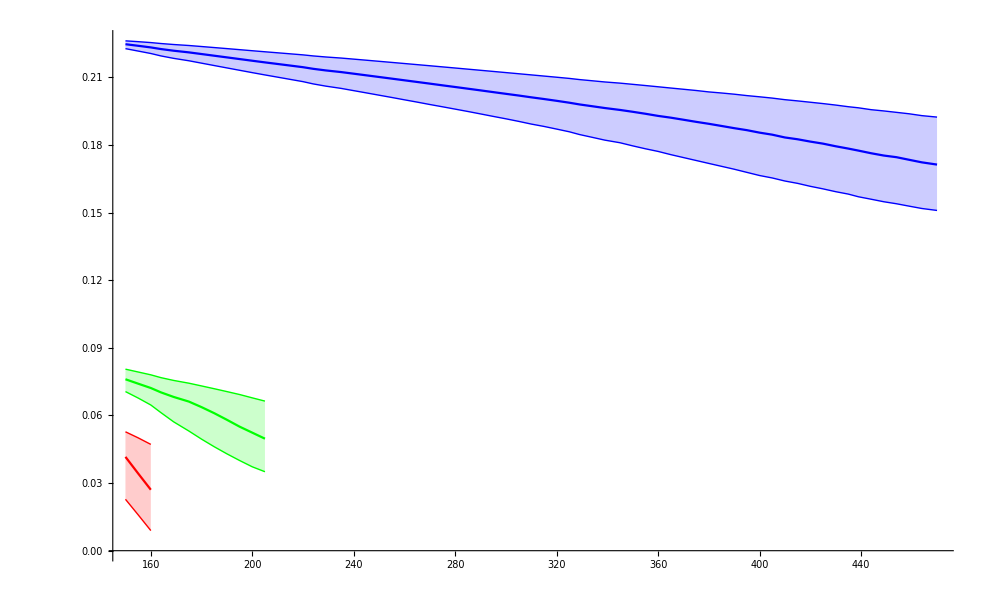

```mathematica
ListPlot[{Transpose[{Tscanb[[;;bb1Tmelt]],areafitbb[[;;bb1Tmelt,1]]}],Transpose[{Tscanb[[;;bb1Tmelt]],areafitbbl[[;;bb1Tmelt,1]]}],Transpose[{Tscanb[[;;bb1Tmelt]],areafitbbu[[;;bb1Tmelt,1]]}],Transpose[{Tscanb[[;;bb2Tmelt]],areafitbb[[;;bb2Tmelt,2]]}],Transpose[{Tscanb[[;;bb2Tmelt]],areafitbbl[[;;bb2Tmelt,2]]}],Transpose[{Tscanb[[;;bb2Tmelt]],areafitbbu[[;;bb2Tmelt,2]]}],Transpose[{Tscanb[[;;bb3Tmelt]],areafitbb[[;;bb3Tmelt,3]]}],Transpose[{Tscanb[[;;bb3Tmelt]],areafitbbl[[;;bb3Tmelt,3]]}],Transpose[{Tscanb[[;;bb3Tmelt]],areafitbbu[[;;bb3Tmelt,3]]}]},PlotRange->All,Filling->{1->{2},1->{3},4->{5},4->{6},7->{8},7->{9}},FillingStyle->Opacity[0.2],PlotStyle->{Blue,{Blue,Thin},{Blue,Thin},Green,{Green,Thin},{Green,Thin},Red,{Red,Thin},{Red,Thin}},Joined->True]
```